#### Problem 10.3.11

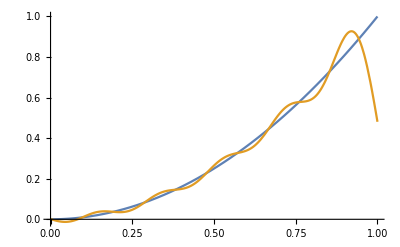

```mathematica
Plot[{Piecewise[{{0, -1≤x<0},{x^2, 0≤x<1}}], (1/6)+Sum[(2*Cos[n*Pi]*Cos[n*Pi*x]/((n*Pi)^2))+((2*Cos[n*Pi]-2-((n*Pi)^2)*Cos[n*Pi])*Sin[n*Pi*x]/((n*Pi)^3)), {n, 10}]}, {x, 0,1}]
```

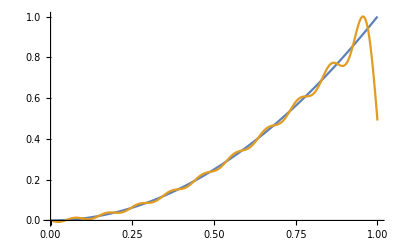

```mathematica
Plot[{Piecewise[{{0, -1≤x<0},{x^2, 0≤x<1}}],  (1/6)+Sum[(2*Cos[n*Pi]*Cos[n*Pi*x]/((n*Pi)^2))+((2*Cos[n*Pi]-2-((n*Pi)^2)*Cos[n*Pi])*Sin[n*Pi*x]/((n*Pi)^3)), {n, 20}]}, {x, 0,1}]
```

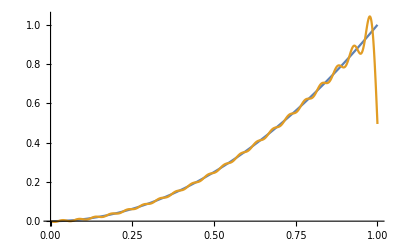

```mathematica
Plot[{Piecewise[{{0, -1≤x<0},{x^2, 0≤x<1}}], (1/6)+Sum[(2*Cos[n*Pi]*Cos[n*Pi*x]/((n*Pi)^2))+((2*Cos[n*Pi]-2-((n*Pi)^2)*Cos[n*Pi])*Sin[n*Pi*x]/((n*Pi)^3)), {n, 40}]}, {x, 0,1}]
```

```mathematica
f[x_]:=Piecewise[{{0, -1≤x<0},{x^2, 0≤x<1}}]
```

```mathematica
g[x_]:=(1/6)+Sum[(2*Cos[n*Pi]*Cos[n*Pi*x]/((n*Pi)^2))+((2*Cos[n*Pi]-2-((n*Pi)^2)*Cos[n*Pi])*Sin[n*Pi*x]/((n*Pi)^3)), {n, 10}]
```

```mathematica
h[x_]:=(1/6)+Sum[(2*Cos[n*Pi]*Cos[n*Pi*x]/((n*Pi)^2))+((2*Cos[n*Pi]-2-((n*Pi)^2)*Cos[n*Pi])*Sin[n*Pi*x]/((n*Pi)^3)), {n, 20}]
```

```mathematica
j[x_]:=(1/6)+Sum[(2*Cos[n*Pi]*Cos[n*Pi*x]/((n*Pi)^2))+((2*Cos[n*Pi]-2-((n*Pi)^2)*Cos[n*Pi])*Sin[n*Pi*x]/((n*Pi)^3)), {n, 40}]
```

```mathematica
N[{1-g[-1],1-h[1],1-j[1]}]
```

{0.519285,0.509883,0.505003}

#### Problem 10.4.27c,d

#### Part C

Cosine Series

```mathematica
gc[x_]:=(3/2)+Sum[(6-6*Cos[n*Pi])*Cos[n*Pi*x/3]/((n*Pi)^2), {n, 2}]
```

```mathematica
hc[x_]:=(3/2)+Sum[(6-6*Cos[n*Pi])*Cos[n*Pi*x/3]/((n*Pi)^2), {n, 3}]
```

```mathematica
ic[x_]:=(3/2)+Sum[(6-6*Cos[n*Pi])*Cos[n*Pi*x/3]/((n*Pi)^2), {n, 4}]
```

```mathematica
jc[x_]:=(3/2)+Sum[(6-6*Cos[n*Pi])*Cos[n*Pi*x/3]/((n*Pi)^2), {n, 5}]
```

```mathematica
fc[x_]:=Piecewise[{{3+x, -3≤x<0},{3-x,0≤x≤3}}]
```

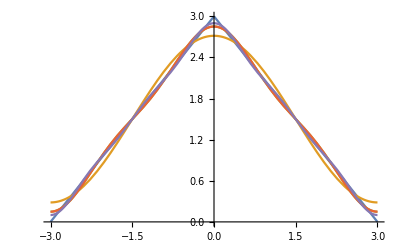

```mathematica
Plot[{fc[x],gc[x],hc[x],ic[x],jc[x]}, {x,-3,3}]
```

Sine Series

```mathematica
gs[x_]:=Sum[6*Sin[n*Pi*x/3]/(n*Pi), {n,2}]
```

```mathematica
hs[x_]:=Sum[6*Sin[n*Pi*x/3]/(n*Pi), {n,3}]
```

```mathematica
is[x_]:=Sum[6*Sin[n*Pi*x/3]/(n*Pi), {n,4}]
```

```mathematica
js[x_]:=Sum[6*Sin[n*Pi*x/3]/(n*Pi), {n,5}]
```

```mathematica
fs[x_]:=Piecewise[{{-3-x,-3≤x<0},{3-x,0≤x≤3}}]
```

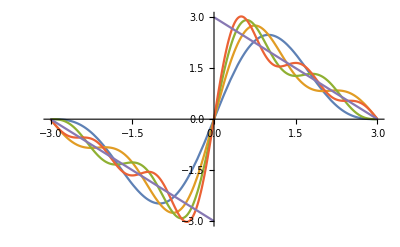

```mathematica
Plot[{gs[x],hs[x],is[x],js[x],fs[x]},{x,-3,3}]
```

#### Part D

```mathematica
Manipulate[Plot[Abs[fc[x]-((3/2)+Sum[(6-6*Cos[n*Pi])*Cos[n*Pi*x/3]/((n*Pi)^2), {n, m}])], {x,0,3}, PlotRange-> {{0,3},{-.5,.5}}], {m,1,100}]
```

```mathematica
Manipulate[N[fc[0]-((3/2)+Sum[(6-6*Cos[n*Pi])*Cos[n*Pi*0/3]/((n*Pi)^2), {n, m}])], {m,1,100}]
```

```mathematica
Manipulate[Plot[Abs[fs[x]-Sum[6*Sin[n*Pi*x/3]/(n*Pi), {n,m}]], {x,0,3},PlotRange-> {{0,3},{-3,3}}], {m,1,100}]
```

```mathematica
Manipulate[N[Abs[fs[0.999]-Sum[6*Sin[n*Pi*0.999/3]/(n*Pi), {n, m}]]], {m,1,100}]
```

```mathematica
fc[0]-gc[0]
```

3/2-12/π^2

```mathematica
N[3/2-12/π^2]
```

0.284146

```mathematica
N[-3/2+12/π^2]
```

-0.284146

```mathematica
gc[0]
```

3/2+12/π^2

```mathematica
N[3/2+12/π^2]
```

2.71585

```mathematica
N[3/2-12/π^2]
```

0.284146

```mathematica
fc[0]
```

3